Model from the 2003 paper “EFFECTS OF FIRE AND HERBIVORY ON THE STABILITY OF SAVANNA ECOSYSTEMS”
Scenario A: Low water influx, water_in=250

Define parameters:

```mathematica
u=0.6;
rh=1.0;
rw=0.5;
dh=0.9;
dw=0.4;
alpha=0.4;
beta=300;
p=1;
```

Define water recharge rates:

```mathematica
win=250;
ws= 0 ;

wt= win-ws;
```

Define system without fire effects-change parameters wt_ and ws_ depending on which scenarios you’re in

```mathematica
dhdt[H_,W_]:=rh*wt*(H)/(H+u*W+p*ws)-dh*H
```

```mathematica
dwdt[H_,W_]:=rw*(wt*(u*W)/(H+u*W+p*ws)+ws)-dw*W
```

Find Fixed points

```mathematica
Simplify[Solve[dhdt[H,W]==0,H]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{H→0.},{H→277.778-0.6 W}}

```mathematica
p1=Plot[277.77777777777777-0.6*W,{W,0,750}];
```

```mathematica
Simplify[Solve[dwdt[H,W]==0,H]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{H→187.5-0.6 W}}

```mathematica
p2=Plot[187.5-0.6* W,{W,0,750},PlotStyle->Red];
```

```mathematica
fp=Simplify[Solve[dwdt[H,W]==0 && dhdt[H,W]==0,{H,W}]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{H→0.,W→312.5},{H→277.778,W→-3.14432×10^-14}}

```mathematica
fp1=Part[fp,1]
```

{H→0.,W→312.5}

```mathematica
fp2=Part[fp,2]
```

{H→277.778,W→-3.14432×10^-14}

```mathematica
p1h=0;
p1w=312.5;

p2h=277.7777777777778;
p2w=0;
```

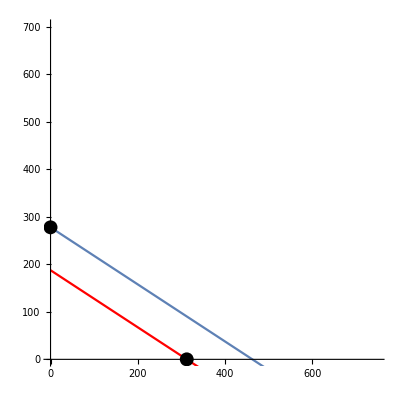

```mathematica
Show[p1,p2,Graphics[{PointSize[0.025],Point[{p1w,p1h}]}],Graphics[{PointSize[0.025],Point[{p2w,p2h}]}],PlotRange->{0,700},AspectRatio->1]
```

Partial Derivatives evaluated at first fixed point: unstable

```mathematica
j11=D[dhdt[H,W],H]/.fp1;
j12=D[dhdt[H,W],W]/.fp1;
j21=D[dwdt[H,W],H]/.fp1;
j22=D[dhdt[H,W],W]/.fp1;
J={{j11,j12},{j21,j22}};
Eigenvalues[J]
Eigenvectors[J];
```

ReplaceAll::reps: {fp1} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

{1/2 ((-(150. W)/(0.6 H+W)^2/.fp1)+(-0.9-(250. W)/(0.6 H+W)^2+250./(0.6 H+W)/.fp1)-√((-(150. W)/(0.6 H+W)^2/.fp1)^2-2 (-(150. W)/(0.6 H+W)^2/.fp1) (-0.9-(250. W)/(0.6 H+W)^2+250./(0.6 H+W)/.fp1)+4 (-0.4-(45. H)/(0.6 H+W)^2+75./(0.6 H+W)/.fp1) (-0.9-(250. W)/(0.6 H+W)^2+250./(0.6 H+W)/.fp1)+(-0.9-(250. W)/(0.6 H+W)^2+250./(0.6 H+W)/.fp1)^2)),1/2 ((-(150. W)/(0.6 H+W)^2/.fp1)+(-0.9-(250. W)/(0.6 H+W)^2+250./(0.6 H+W)/.fp1)+√((-(150. W)/(0.6 H+W)^2/.fp1)^2-2 (-(150. W)/(0.6 H+W)^2/.fp1) (-0.9-(250. W)/(0.6 H+W)^2+250./(0.6 H+W)/.fp1)+4 (-0.4-(45. H)/(0.6 H+W)^2+75./(0.6 H+W)/.fp1) (-0.9-(250. W)/(0.6 H+W)^2+250./(0.6 H+W)/.fp1)+(-0.9-(250. W)/(0.6 H+W)^2+250./(0.6 H+W)/.fp1)^2))}

0.

-0.666667

0.

{{0.433333,0.},{-0.666667,0.}}

{0.433333,0.}

{{0.544988,-0.838444},{0.,1.}}

Partial Derivatives evaluated at second fixed point: stable

```mathematica
j11=D[dhdt[H,W],H]/.fp2
```

-0.9

```mathematica
j12=D[dhdt[H,W],W]/.fp2
```

-0.54

```mathematica
j21=D[dwdt[H,W],H]/.fp2
```

3.05628×10^-17

```mathematica
j22=D[dhdt[H,W],W]/.fp2
```

-0.54

```mathematica
J={{j11,j12},{j21,j22}}
Eigenvalues[J]
Eigenvectors[J]
```

{{-0.9,-0.54},{3.05628×10^-17,-0.54}}

{-0.9,-0.54}

{{1.,0.},{-0.83205,0.5547}}